```mathematica
SingleGradientDescent[f_, steps_, d_,ogpoint_]:=Module[
{point=ogpoint,temp=0.1, prevloss=f[ogpoint], loss=f[ogpoint], gradient, prevpoint},
Do[
prevpoint=point;
gradient=(Table[f[point-d*UnitVector[Length[point], i]], {i, Length[point]}]-loss)/d;
point-=gradient*temp;
prevloss=loss;
loss=f[point];
If[prevloss>loss, point=prevpoint;temp*=0.5;,temp*=1.1];
, {step, steps}];
Return[point];
]

GradientDescent[f_, bounds_, numpoints_:1000,steps_:100, d_:10^-10]:=Module[{points=Transpose[Table[RandomReal[bound, 10*numpoints], {bound, bounds}]], threshold},

threshold=Min[f/@RandomChoice[points, 10]];
points=ParallelTable[If[f[point]<threshold, point, Nothing], {point, points}];

points=ParallelTable[SingleGradientDescent[f, steps, d, point], {point, points}];
First[MinimalBy[points, f]]]
```

```mathematica
GradientDescent[-(#[[1]]-0.2)^2-(#[[2]]-Pi)^2&, {{0, 1}, {0, 1}}]
```

{0.2,3.14159}

```mathematica
NOT[x_]:=1-x
AND[x_, y_]:=x y
OR[x_, y_]:=NOT[AND[NOT[x], NOT[y]]]
XOR[x_, y_]:=AND[NOT[AND[x, y]], OR[x, y]]
t1=XOR[a, XOR[b, XOR[c, XOR[d, e]]]];
t2=OR[a, OR[b, OR[c, OR[d, e]]]];
code20=XOR[t1, t2]
```

(1-(1-(1-a) (1-b) (1-c) (1-d) (1-e)) (1-a (1-b (1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))) (1-(1-b) (1-(1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))))) (1-(1-a) (1-(1-b (1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))) (1-(1-b) (1-(1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))))))) (1-(1-a) (1-b) (1-c) (1-d) (1-e) (1-(1-a (1-b (1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))) (1-(1-b) (1-(1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))))) (1-(1-a) (1-(1-b (1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))) (1-(1-b) (1-(1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))))))))

```mathematica
Code20Single=FunctionCompile[Function[{Typed[a, "Real64"], Typed[b, "Real64"], Typed[c, "Real64"], Typed[d, "Real64"], Typed[e, "Real64"]},

((1-(1-(1-a) (1-b) (1-c) (1-d) (1-e)) (1-a (1-b (1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))) (1-(1-b) (1-(1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))))) (1-(1-a) (1-(1-b (1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))) (1-(1-b) (1-(1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))))))) (1-(1-a) (1-b) (1-c) (1-d) (1-e) (1-(1-a (1-b (1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))) (1-(1-b) (1-(1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))))) (1-(1-a) (1-(1-b (1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e)))) (1-(1-b) (1-(1-c (1-(1-d) (1-e)) (1-d e)) (1-(1-c) (1-(1-(1-d) (1-e)) (1-d e))))))))))^2

], CompilerOptions->{"LLVMOptimization"->"ClangOptimization"[3], "AbortHandling"->False, "OptimizationLevel"->3,"InvocationMode"->"Standalone"}];
```

```mathematica
WindowsPaddedZero[list_]:=With[{l=Join[list[[-2;;]], list, list[[;;2]]]}, Table[l[[i;;i+4]], {i, Length[l]-4}]]
```

```mathematica
Code20Row[list_]:=Code20Single@@@WindowsPaddedZero[list]
```

```mathematica
rand=RandomReal[{0, 1}, 1000];
RepeatedTiming[Nest[Code20Row, rand, 100]]//First
```

0.0515873

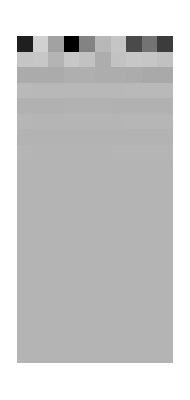

```mathematica
ArrayPlot[NestList[Code20Row,RandomReal[{0, 1}, 10],20]]
```

```mathematica
Variance[Nest[Code20Row,RandomReal[{0, 1}, 10],20]]
```

4.79441×10^-19

```mathematica
MaximalBy[RandomReal[{0, 1}, {100, 10}],Variance[Nest[Code20Row,#,5]]&]
```

{{0.986546,0.799352,0.0316861,0.988689,0.760933,0.180197,0.626391,0.071356,0.725135,0.888571}}

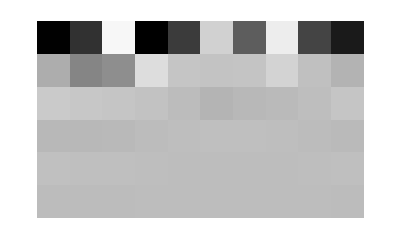

```mathematica
ArrayPlot[NestList[Code20Row,//First,5]]
```

```mathematica
GradientDescent[If[Min[#]>=0&&Max[#]<=1,-(Variance[Nest[Code20Row,#,2]]), 0]&, ConstantArray[{0, 1}, 10], 1000, 1000]
```

{-976450.,-976450.,-976450.,-976450.,-976450.,-976450.,-976450.,-976450.,-976450.,-976450.}

CompiledCodeFunction::uncomp: A compiled code runtime error occurred; reverting to uncompiled evaluation: FloatingPointOverflow.

General::stop: Further output of CompiledCodeFunction::uncomp will be suppressed during this calculation.

CompiledCodeFunction::argtype: Argument type at position 1 does not match function signature.

General::stop: Further output of CompiledCodeFunction::argtype will be suppressed during this calculation.

1/90 (Conjugate[Failure[…]] (9 Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…])+Conjugate[Failure[…]] (-Failure[…]+9 Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…])+Conjugate[Failure[…]] (-Failure[…]-Failure[…]+9 Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…])+Conjugate[Failure[…]] (-Failure[…]-Failure[…]-Failure[…]+9 Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…])+Conjugate[Failure[…]] (-Failure[…]-Failure[…]-Failure[…]-Failure[…]+9 Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…])+Conjugate[Failure[…]] (-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]+9 Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…])+Conjugate[Failure[…]] (-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]+9 Failure[…]-Failure[…]-Failure[…]-Failure[…])+Conjugate[Failure[…]] (-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]+9 Failure[…]-Failure[…]-Failure[…])+Conjugate[Failure[…]] (-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]+9 Failure[…]-Failure[…])+Conjugate[Failure[…]] (-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]-Failure[…]+9 Failure[…]))

CompiledCodeFunction::uncomp: A compiled code runtime error occurred; reverting to uncompiled evaluation: FloatingPointOverflow.

General::stop: Further output of CompiledCodeFunction::uncomp will be suppressed during this calculation.

CompiledCodeFunction::argtype: Argument type at position 1 does not match function signature.

General::stop: Further output of CompiledCodeFunction::argtype will be suppressed during this calculation.

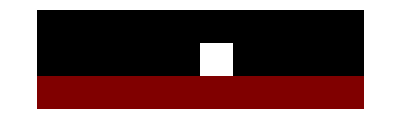

```mathematica
Variance[Nest[Code20Row,,2]]
ArrayPlot[NestList[Code20Row,,2]]
```

```mathematica
Plot3D[Variance[Nest[Code20Row,{1, 0, 1, 1, 1, 1, a, b},3]]^0.1, {a, 0, 1}, {b, 0, 1}, PlotRange->All]
```

-Graphics3D-